#### Define equations

```mathematica
eqns = {m1 x''[t] + k1 x[t] +c1 x'[t]+ k2 (x[t]-y[t])+c2 (x'[t]-y'[t])==0,m2 y''[t] + k2(y[t]-x[t])+c2 (y'[t]-x'[t])==0};
```

#### Solve for specific parameters

```mathematica
analsol = Flatten@Block[{m1= 4,m2=10,k1=100,k2=150,c1 = 0.1,c2 = 0.2 },DSolve[eqns∪{x[0]== 0,y[0]==1,x'[0]==0,y'[0]==0},{x,y},{t,0,1000}]]
```

{x→Function[{t},(0.558629-1.04974×10^-18 ⅈ) ⅇ^(-0.00284796 t) Cos[2.27721 t]-(0.558629-1.04974×10^-18 ⅈ) ⅇ^(-0.044652 t) Cos[8.50366 t]+(0.000885772-3.02671×10^-17 ⅈ) ⅇ^(-0.00284796 t) Sin[2.27721 t]-(0.00298343-8.11043×10^-18 ⅈ) ⅇ^(-0.044652 t) Sin[8.50366 t]],y→Function[{t},(0.853797-3.88743×10^-19 ⅈ) ⅇ^(-0.00284796 t) Cos[2.27721 t]+(0.146203+3.88743×10^-19 ⅈ) ⅇ^(-0.044652 t) Cos[8.50366 t]+(0.00159516-4.6262×10^-17 ⅈ) ⅇ^(-0.00284796 t) Sin[2.27721 t]+(0.000626474+1.23905×10^-17 ⅈ) ⅇ^(-0.044652 t) Sin[8.50366 t]]}

```mathematica
(*numsol = Flatten@Block[{m1=3,m2=3,k1=5,k2=2},NDSolve[eqns∪{x[0]== 0,y[0]==1,x'[0]==0,y'[0]==0},{x,y},{t,0,10}]]*)
```

```mathematica
Attributes@Re
```

{Listable,NumericFunction,Protected}

```mathematica
?Re
```

RowBox[{"Re", "[", StyleBox["z", "TI"], "]"}] gives the real part of the complex number StyleBox["z", "TI"].

```mathematica
?Array
```

RowBox[{"Array", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["n", "TI"]}], "]"}] generates a list of length StyleBox["n", "TI"], with elements RowBox[{StyleBox["f", "TI"], "[", StyleBox["i", "TI"], "]"}]. 
RowBox[{"Array", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["n", "TI"], ",", StyleBox["r", "TI"]}], "]"}] generates a list using the index origin StyleBox["r", "TI"].
RowBox[{"Array", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["n", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["a", "TI"], ",", StyleBox["b", "TI"]}], "}"}]}], "]"}] generates a list using StyleBox["n", "TI"] values from StyleBox["a", "TI"] to StyleBox["b", "TI"].
RowBox[{"Array", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["n", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["n", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] generates an SubscriptBox[StyleBox["n", "TI"], StyleBox["1", "TR"]]×SubscriptBox[StyleBox["n", "TI"], StyleBox["2", "TR"]]×… array of nested lists, with elements RowBox[{StyleBox["f", "TI"], "[", RowBox[{SubscriptBox[StyleBox["i", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "]"}]. 
RowBox[{"Array", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["n", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["n", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["r", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["r", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] generates a list using the index origins SubscriptBox[StyleBox["r", "TI"], StyleBox["i", "TI"]] (default 1). 
RowBox[{"Array", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["n", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["n", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["a", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["b", "TI"], StyleBox["1", "TR"]]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["a", "TI"], StyleBox["2", "TR"]], ",", SubscriptBox[StyleBox["b", "TI"], StyleBox["2", "TR"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] generates a list using SubscriptBox[StyleBox["n", "TI"], StyleBox["i", "TI"]] values from SubscriptBox[StyleBox["a", "TI"], StyleBox["i", "TI"]] to SubscriptBox[StyleBox["b", "TI"], StyleBox["i", "TI"]].
RowBox[{"Array", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["dims", "TI"], ",", StyleBox["origin", "TI"], ",", StyleBox["h", "TI"]}], "]"}] uses head StyleBox["h", "TI"], rather than List, for each level of the array.

```mathematica
?Table
```

RowBox[{"Table", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", SubscriptBox[StyleBox["i", "TI"], StyleBox["max", "TI"]], "}"}]}], "]"}] generates a list of SubscriptBox[StyleBox["i", "TI"], StyleBox["max", "TI"]] copies of StyleBox["expr", "TI"]. 
RowBox[{"Table", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["i", "TI"], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] generates a list of the values of StyleBox["expr", "TI"] when StyleBox["i", "TI"] runs from 1 to SubscriptBox[StyleBox["i", "TI"], StyleBox["max", "TI"]]. 
RowBox[{"Table", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["i", "TI"], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] starts with RowBox[{StyleBox["i", "TI"], "=", SubscriptBox[StyleBox["i", "TI"], StyleBox["min", "TI"]]}]. 
RowBox[{"Table", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["i", "TI"], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["max", "TI"]], ",", StyleBox["di", "TI"]}], "}"}]}], "]"}] uses steps StyleBox["di", "TI"]. 
RowBox[{"Table", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["i", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["i", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "}"}]}], "]"}] uses the successive values SubscriptBox[StyleBox["i", "TI"], StyleBox["1", "TR"]], SubscriptBox[StyleBox["i", "TI"], StyleBox["2", "TR"]], ….
RowBox[{"Table", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["i", "TI"], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["i", "TI"], StyleBox["max", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["j", "TI"], ",", SubscriptBox[StyleBox["j", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["j", "TI"], StyleBox["max", "TI"]]}], "}"}], ",", StyleBox["…", "TR"]}], "]"}] gives a nested list. The list associated with StyleBox["i", "TI"] is outermost.

```mathematica
Re@Through[({x,y}/.analsol)[{0.1}]]
```

{{0.17513},{0.928368}}

```mathematica
Flatten@Table[Re@((x/.analsol)[{i}]),{i,0,10,0.01}]
```

{0.,0.0018732,0.00747591,0.0167612,0.0296537,0.0460499,0.0658195,0.0888057,0.114827,0.143677,0.17513,0.208936,0.24483,0.282527,0.32173,0.362129,0.403401,0.44522,0.48725,0.529154,0.570596,0.611239,0.650752,0.68881,0.725097,0.759309,0.791156,0.820363,0.846673,0.869847,0.88967,0.905949,0.918513,0.92722,0.931953,0.932621,0.929163,0.921546,0.909766,0.893847,0.873843,0.849833,0.821928,0.790264,0.755001,0.716327,0.674452,0.629608,0.582046,0.532038,0.479871,0.425846,0.370278,0.313491,0.255817,0.197593,0.13916,0.0808586,0.0230281,-0.0339964,-0.0898864,-0.144323,-0.196996,-0.247613,-0.295893,-0.341574,-0.384413,-0.424188,-0.460699,-0.493771,-0.523254,-0.549021,-0.570976,-0.589049,-0.603197,-0.613406,-0.61969,-0.622092,-0.620681,-0.615554,-0.606836,-0.594675,-0.579243,-0.560737,-0.539375,-0.515393,-0.489047,-0.460608,-0.430363,-0.398608,-0.365651,-0.331808,-0.297398,-0.262745,-0.228171,-0.194,-0.160548,-0.128126,-0.0970362,-0.0675699,-0.0400047,-0.0146034,0.00838877,0.0287451,0.0462595,0.0607482,0.0720506,0.0800308,0.0845784,0.0856094,0.0830669,0.0769211,0.0671702,0.0538398,0.036983,0.0166799,-0.0069629,-0.0338129,-0.0637132,-0.0964829,-0.131919,-0.169798,-0.209876,-0.251893,-0.295573,-0.340626,-0.38675,-0.433636,-0.480966,-0.528416,-0.575663,-0.622381,-0.668247,-0.712943,-0.756157,-0.797588,-0.836943,-0.873945,-0.908331,-0.939856,-0.968294,-0.993438,-1.0151,-1.03313,-1.04739,-1.05776,-1.06416,-1.06654,-1.06486,-1.05912,-1.04935,-1.0356,-1.01794,-0.99648,-0.971355,-0.942718,-0.910746,-0.875641,-0.837624,-0.796935,-0.753832,-0.708589,-0.661493,-0.612841,-0.562942,-0.512109,-0.460664,-0.408927,-0.357222,-0.305869,-0.255183,-0.205475,-0.157045,-0.110184,-0.0651668,-0.0222567,0.0183013,0.0562805,0.0914743,0.123698,0.152788,0.178607,0.201042,0.220004,0.235431,0.24729,0.25557,0.260291,0.261497,0.25926,0.253677,0.244869,0.232981,0.218183,0.200664,0.180633,0.15832,0.133969,0.107841,0.0802097,0.0513582,0.0215801,-0.00882462,-0.0395517,-0.0702944,-0.100746,-0.130602,-0.159563,-0.187336,-0.213635,-0.238189,-0.260735,-0.28103,-0.298843,-0.313964,-0.326203,-0.33539,-0.341379,-0.344046,-0.343293,-0.339046,-0.331258,-0.319909,-0.305002,-0.286569,-0.264668,-0.239382,-0.21082,-0.179115,-0.144422,-0.106921,-0.0668111,-0.0243117,0.0203398,0.0668894,0.115069,0.164597,0.215183,0.266525,0.318317,0.370249,0.422007,0.473278,0.523753,0.573126,0.621097,0.667377,0.711688,0.753762,0.79335,0.830216,0.864145,0.89494,0.922426,0.94645,0.966883,0.983621,0.996583,1.00572,1.01099,1.0124,1.00998,1.00377,0.993851,0.980319,0.963301,0.942945,0.919419,0.892914,0.863641,0.831827,0.797717,0.761569,0.723654,0.684255,0.643661,0.60217,0.560083,0.517702,0.475331,0.433272,0.391819,0.351264,0.311887,0.273959,0.237738,0.203467,0.171375,0.141669,0.114541,0.0901591,0.0686724,0.0502051,0.0348585,0.0227092,0.0138089,0.00818414,0.00583592,0.00673987,0.0108465,0.0180814,0.0283461,0.0415188,0.0574548,0.0759883,0.0969334,0.120085,0.145221,0.172104,0.200482,0.230091,0.260658,0.291901,0.323533,0.355261,0.386793,0.417835,0.448098,0.477296,0.50515,0.53139,0.555758,0.578007,0.597905,0.615237,0.629805,0.641431,0.649957,0.655247,0.657186,0.655687,0.650682,0.642132,0.630021,0.614357,0.595176,0.572537,0.546524,0.517245,0.484832,0.449436,0.411234,0.370419,0.327205,0.281821,0.234512,0.185538,0.13517,0.0836874,0.0313797,-0.0214588,-0.0745299,-0.127534,-0.180171,-0.232145,-0.283164,-0.332941,-0.381202,-0.427679,-0.47212,-0.514286,-0.553954,-0.590919,-0.624994,-0.656013,-0.683833,-0.708331,-0.729408,-0.746989,-0.761024,-0.771487,-0.778377,-0.781718,-0.781558,-0.777969,-0.771048,-0.760913,-0.747705,-0.731585,-0.712734,-0.691352,-0.667656,-0.641875,-0.614255,-0.585051,-0.554531,-0.522968,-0.490641,-0.457834,-0.424831,-0.391918,-0.359375,-0.327481,-0.296506,-0.266713,-0.238353,-0.211665,-0.186875,-0.164193,-0.143811,-0.125903,-0.110623,-0.0981041,-0.0884578,-0.0817724,-0.0781132,-0.0775215,-0.0800147,-0.0855858,-0.0942038,-0.105814,-0.120338,-0.137674,-0.157699,-0.180269,-0.205218,-0.232363,-0.261503,-0.292419,-0.32488,-0.358641,-0.393446,-0.42903,-0.465119,-0.501437,-0.537703,-0.573633,-0.608946,-0.643364,-0.676613,-0.708426,-0.738545,-0.766723,-0.792724,-0.816329,-0.837331,-0.855543,-0.870796,-0.882942,-0.89185,-0.897416,-0.899555,-0.898207,-0.893335,-0.884925,-0.87299,-0.857564,-0.838706,-0.816497,-0.791044,-0.762473,-0.730932,-0.696589,-0.65963,-0.62026,-0.5787,-0.535183,-0.489959,-0.443285,-0.395428,-0.346666,-0.297276,-0.247544,-0.197755,-0.148192,-0.0991369,-0.0508673,-0.0036532,0.0422439,0.0865727,0.129094,0.169583,0.20783,0.243642,0.276844,0.307281,0.334818,0.359342,0.380762,0.399009,0.414039,0.425829,0.434381,0.43972,0.441896,0.440978,0.43706,0.430259,0.420708,0.408563,0.393997,0.377201,0.358382,0.337759,0.315565,0.292043,0.267445,0.242031,0.216066,0.189815,0.163549,0.137535,0.112038,0.0873177,0.0636284,0.0412149,0.0203121,0.00114254,-0.0160847,-0.0311758,-0.0439538,-0.0542593,-0.0619524,-0.0669131,-0.0690425,-0.0682636,-0.0645214,-0.057784,-0.0480423,-0.0353102,-0.0196248,-0.00104557,0.0203454,0.0444445,0.0711271,0.100248,0.131645,0.165135,0.20052,0.237588,0.27611,0.315849,0.356556,0.397972,0.439833,0.481871,0.523814,0.565388,0.606324,0.646352,0.685209,0.722639,0.758392,0.792233,0.823936,0.853289,0.880096,0.904178,0.925373,0.943539,0.958552,0.970313,0.978741,0.983778,0.98539,0.983565,0.978314,0.96967,0.95769,0.942452,0.924057,0.902626,0.878298,0.851235,0.821613,0.789626,0.755485,0.71941,0.681638,0.642412,0.601987,0.560621,0.518581,0.476134,0.433548,0.391091,0.349029,0.307621,0.267122,0.227777,0.18982,0.153475,0.118952,0.086446,0.0561364,0.0281842,0.00273239,-0.0200958,-0.0401974,-0.0574908,-0.0719159,-0.0834345,-0.092031,-0.0977117,-0.100506,-0.100463,-0.0976565,-0.0921791,-0.0841442,-0.0736845,-0.0609512,-0.0461125,-0.0293527,-0.0108705,0.00912233,0.0304025,0.0527369,0.0758844,0.0995976,0.123625,0.147711,0.171601,0.195042,0.217782,0.239575,0.260182,0.279372,0.296925,0.312631,0.326296,0.337739,0.346795,0.353318,0.357177,0.358266,0.356493,0.351792,0.344116,0.333439,0.319758,0.303093,0.283485,0.260995,0.235709,0.20773,0.177182,0.14421,0.108973,0.071651,0.0324368,-0.00846132,-0.0508226,-0.0944152,-0.138998,-0.184321,-0.230129,-0.276162,-0.322159,-0.367858,-0.412996,-0.457315,-0.500564,-0.542494,-0.58287,-0.621462,-0.658056,-0.692449,-0.724453,-0.753896,-0.780625,-0.804503,-0.825413,-0.843258,-0.857962,-0.869471,-0.877752,-0.882792,-0.884602,-0.883214,-0.878681,-0.871078,-0.860499,-0.847059,-0.830892,-0.812148,-0.790995,-0.767616,-0.74221,-0.714985,-0.686164,-0.655977,-0.624662,-0.592464,-0.559632,-0.526417,-0.493072,-0.459847,-0.426989,-0.394743,-0.363344,-0.333021,-0.303992,-0.276465,-0.250633,-0.226676,-0.204759,-0.185028,-0.167613,-0.152624,-0.140154,-0.130274,-0.123033,-0.118462,-0.116568,-0.117339,-0.120742,-0.126721,-0.135202,-0.146089,-0.15927,-0.174612,-0.191966,-0.211166,-0.232032,-0.254371,-0.277977,-0.302634,-0.328115,-0.354188,-0.380615,-0.407154,-0.43356,-0.459589,-0.484998,-0.509546,-0.533,-0.55513,-0.575719,-0.594555,-0.611442,-0.626194,-0.638641,-0.648628,-0.656017,-0.660688,-0.662539,-0.661489,-0.657475,-0.650456,-0.640411,-0.62734,-0.611266,-0.59223,-0.570295,-0.545544,-0.518081,-0.488026,-0.45552,-0.420718,-0.383795,-0.344936,-0.304343,-0.262229,-0.218816,-0.174337,-0.129031,-0.0831427,-0.0369215,0.0093822,0.0555172,0.101234,0.146286,0.190431,0.233436,0.275073,0.315127,0.35339,0.389673,0.423795,0.455595,0.484926,0.511659,0.535684,0.55691,0.575265,0.590698,0.603178,0.612695,0.61926,0.622903,0.623676,0.62165,0.616916,0.609582,0.599776,0.587641,0.573335,0.557033,0.538921,0.519198,0.498072,0.475762,0.452491,0.42849,0.403992,0.379235,0.354453,0.329881,0.305752,0.282292,0.25972,0.238251,0.218084,0.199413,0.182415,0.167256,0.154085,0.143036,0.134226,0.127752,0.123695,0.122116,0.123055,0.126533,0.132552,0.141091,0.152111,0.165554,0.18134,0.199373,0.219538,0.241703,0.265718,0.291422,0.318635,0.347168,0.37682,0.40738,0.438628,0.470338,0.502278,0.534216,0.565913,0.597135,0.627646,0.657217,0.685621,0.71264,0.738062,0.761687,0.783325,0.802801,0.81995,0.834625,0.846695,0.856046,0.862581,0.866222,0.866912,0.864611,0.859301,0.850982,0.839677,0.825426,0.808291,0.788351,0.765706,0.740472,0.712782,0.682787,0.650651,0.616554,0.580687,0.543252,0.504462,0.464537,0.423706,0.382201,0.340257,0.298113,0.256006,0.214173,0.172847,0.132255,0.0926204,0.0541556,0.0170646,-0.0184594,-0.052236,-0.084098,-0.113893,-0.141485,-0.166755,-0.189599,-0.209934,-0.227695,-0.242836,-0.25533,-0.265171,-0.272371,-0.276962,-0.278995,-0.278541,-0.275687,-0.27054,-0.26322,-0.253867,-0.242633,-0.229683,-0.215195,-0.19936,-0.182375,-0.164448,-0.14579,-0.12662,-0.107158,-0.0876287,-0.0682531,-0.0492524,-0.0308441,-0.0132408,0.00335148,0.0187348,0.0327208,0.0451319,0.0558027,0.0645816,0.0713311,0.0759296,0.078272,0.0782704,0.0758547,0.0709735,0.0635941,0.0537031,0.041306,0.0264279,0.00911258,-0.0105772,-0.0325604,-0.0567384,-0.0829953,-0.111199,-0.141203,-0.172845,-0.20595,-0.240333,-0.275796,-0.312133,-0.349131,-0.386569,-0.424224,-0.461868,-0.499272,-0.536208,-0.57245,-0.607776,-0.641966,-0.674811,-0.706107,-0.735662,-0.763292,-0.788829,-0.812116,-0.833011,-0.851387,-0.867136,-0.880164,-0.890397,-0.897778,-0.902271,-0.903857,-0.902536,-0.898329,-0.891274,-0.881429,-0.86887,-0.853689,-0.835997,-0.815921,-0.793602,-0.769195,-0.742871,-0.71481,-0.685203,-0.65425,-0.622159,-0.589145,-0.555427,-0.521227,-0.486768,-0.452273,-0.417965,-0.38406,-0.350774,-0.318312,-0.286874,-0.25665,-0.227819,-0.200548,-0.174992,-0.151291,-0.12957,-0.109938,-0.0924863,-0.0772909,-0.0644086,-0.0538782,-0.0457199,-0.0399354,-0.0365081}

```mathematica
Flatten@Table[Re@((y/.analsol)[{i}]),{i,0,10,0.01}]
```

{1.,0.999251,0.997007,0.993281,0.988095,0.981475,0.973459,0.964087,0.95341,0.941483,0.928368,0.914134,0.898852,0.882599,0.865458,0.847513,0.828852,0.809565,0.789744,0.769482,0.748872,0.728006,0.706978,0.685876,0.664791,0.643807,0.623007,0.602469,0.582267,0.562471,0.543143,0.524341,0.506118,0.488519,0.471583,0.45534,0.439815,0.425025,0.410981,0.397684,0.38513,0.373306,0.362194,0.351767,0.341992,0.332831,0.324239,0.316164,0.308551,0.30134,0.294466,0.287861,0.281452,0.275167,0.268929,0.262661,0.256285,0.249722,0.242896,0.235731,0.228151,0.220085,0.211464,0.202221,0.192297,0.181633,0.170178,0.157886,0.144716,0.130634,0.115613,0.0996322,0.0826771,0.0647417,0.0458267,0.0259401,0.00509763,-0.0166781,-0.0393569,-0.0629019,-0.0872692,-0.112408,-0.138262,-0.164769,-0.191859,-0.219461,-0.247495,-0.275881,-0.304531,-0.333358,-0.362271,-0.391176,-0.41998,-0.448586,-0.476902,-0.504832,-0.532284,-0.559166,-0.58539,-0.610871,-0.635526,-0.659279,-0.682055,-0.703787,-0.724413,-0.743876,-0.762127,-0.779121,-0.794823,-0.809203,-0.822238,-0.833915,-0.844225,-0.853169,-0.860755,-0.866997,-0.871917,-0.875545,-0.877915,-0.879071,-0.87906,-0.877936,-0.875759,-0.872592,-0.868503,-0.863566,-0.857854,-0.851446,-0.844422,-0.836865,-0.828855,-0.820477,-0.811813,-0.802944,-0.79395,-0.78491,-0.775898,-0.766987,-0.758245,-0.749736,-0.74152,-0.73365,-0.726176,-0.71914,-0.712579,-0.706523,-0.700997,-0.696016,-0.691592,-0.687728,-0.684419,-0.681655,-0.679418,-0.677686,-0.676427,-0.675604,-0.675176,-0.675094,-0.675305,-0.675752,-0.676371,-0.677097,-0.677861,-0.67859,-0.679211,-0.679647,-0.679821,-0.679656,-0.679075,-0.678001,-0.676359,-0.674076,-0.671081,-0.667306,-0.662688,-0.657166,-0.650685,-0.643194,-0.634649,-0.62501,-0.614245,-0.602326,-0.589234,-0.574956,-0.559486,-0.542825,-0.52498,-0.505967,-0.485809,-0.464535,-0.442181,-0.418789,-0.39441,-0.369097,-0.342913,-0.315922,-0.288197,-0.259813,-0.230849,-0.201388,-0.171517,-0.141324,-0.110898,-0.0803319,-0.0497166,-0.0191444,0.0112933,0.0415065,0.0714065,0.100907,0.129926,0.158381,0.186199,0.213307,0.239639,0.265132,0.289733,0.313389,0.336058,0.357704,0.378294,0.397806,0.416224,0.433537,0.449742,0.464845,0.478856,0.491792,0.503679,0.514546,0.524431,0.533375,0.541425,0.548635,0.55506,0.560762,0.565803,0.570253,0.574179,0.577654,0.580749,0.583538,0.586095,0.588492,0.590802,0.593094,0.595436,0.597896,0.600533,0.603408,0.606574,0.610082,0.613976,0.618296,0.623076,0.628344,0.634122,0.640425,0.647263,0.654639,0.662547,0.670978,0.679914,0.689332,0.699202,0.709488,0.720148,0.731136,0.742398,0.753878,0.765514,0.77724,0.788988,0.800684,0.812254,0.823622,0.834709,0.845437,0.855727,0.865499,0.874675,0.88318,0.890938,0.897877,0.903928,0.909026,0.91311,0.916122,0.918011,0.91873,0.918238,0.9165,0.913487,0.909177,0.903555,0.896611,0.888343,0.878757,0.867864,0.855682,0.842238,0.827562,0.811694,0.794677,0.776561,0.757403,0.737263,0.716206,0.694303,0.671626,0.648254,0.624265,0.599743,0.574769,0.54943,0.523812,0.497999,0.472077,0.446131,0.420241,0.39449,0.368954,0.343707,0.318821,0.294362,0.270391,0.246967,0.22414,0.201958,0.18046,0.159681,0.139649,0.120386,0.101906,0.084219,0.0673264,0.0512242,0.0359017,0.0213421,0.00752251,-0.00558565,-0.0180165,-0.0298094,-0.0410084,-0.0516621,-0.0618231,-0.0715475,-0.0808946,-0.089926,-0.0987058,-0.107299,-0.115773,-0.124194,-0.132628,-0.141143,-0.149803,-0.15867,-0.167807,-0.177272,-0.187118,-0.197399,-0.208161,-0.219446,-0.231293,-0.243734,-0.256797,-0.270502,-0.284865,-0.299895,-0.315596,-0.331963,-0.348988,-0.366654,-0.384938,-0.403813,-0.423243,-0.44319,-0.463606,-0.48444,-0.505638,-0.527137,-0.548873,-0.570778,-0.59278,-0.614804,-0.636772,-0.658606,-0.680227,-0.701551,-0.7225,-0.742991,-0.762946,-0.782284,-0.800931,-0.818811,-0.835855,-0.851993,-0.867163,-0.881306,-0.894366,-0.906294,-0.917047,-0.926586,-0.934878,-0.941898,-0.947627,-0.95205,-0.955161,-0.956961,-0.957455,-0.956657,-0.954586,-0.951268,-0.946734,-0.941023,-0.934177,-0.926245,-0.917279,-0.907338,-0.896484,-0.884781,-0.872299,-0.859108,-0.845282,-0.830896,-0.816026,-0.800748,-0.78514,-0.769278,-0.753237,-0.737091,-0.720911,-0.704766,-0.688722,-0.672842,-0.657185,-0.641805,-0.626751,-0.612068,-0.597797,-0.58397,-0.570616,-0.557758,-0.545412,-0.533589,-0.522292,-0.511521,-0.501266,-0.491515,-0.482249,-0.473441,-0.465062,-0.457077,-0.449445,-0.442122,-0.435059,-0.428204,-0.421502,-0.414895,-0.408321,-0.40172,-0.395028,-0.388181,-0.381114,-0.373763,-0.366066,-0.357961,-0.349387,-0.340288,-0.330607,-0.320295,-0.309303,-0.297587,-0.285108,-0.271832,-0.25773,-0.242779,-0.226959,-0.210259,-0.192672,-0.174198,-0.154844,-0.134621,-0.113548,-0.0916495,-0.0689552,-0.0455014,-0.0213302,0.00351149,0.0289714,0.0549924,0.0815132,0.108468,0.135789,0.163402,0.191233,0.219205,0.247239,0.275254,0.303169,0.330903,0.358376,0.385507,0.412218,0.438431,0.464072,0.48907,0.513356,0.536866,0.559539,0.581319,0.602155,0.622001,0.640816,0.658566,0.675222,0.690759,0.705163,0.718422,0.730531,0.741492,0.751313,0.760009,0.767598,0.774107,0.779567,0.784012,0.787486,0.790032,0.791701,0.792547,0.792626,0.791998,0.790726,0.788873,0.786506,0.78369,0.780494,0.776984,0.773227,0.769288,0.765231,0.761118,0.757009,0.752959,0.749023,0.745249,0.741683,0.738365,0.735332,0.732615,0.73024,0.728226,0.72659,0.72534,0.724479,0.724006,0.723913,0.724186,0.724806,0.725749,0.726984,0.728477,0.73019,0.732077,0.734093,0.736184,0.738296,0.740372,0.742351,0.744173,0.745772,0.747085,0.748046,0.748591,0.748655,0.748174,0.747087,0.745332,0.742853,0.739595,0.735505,0.730536,0.724645,0.717792,0.709943,0.701067,0.691142,0.680148,0.668073,0.654909,0.640655,0.625317,0.608905,0.591436,0.572933,0.553425,0.532945,0.511533,0.489235,0.466099,0.442181,0.417539,0.392235,0.366336,0.33991,0.31303,0.28577,0.258205,0.230413,0.202471,0.174457,0.146449,0.118524,0.0907581,0.0632249,0.0359964,0.00914171,-0.0172729,-0.0431848,-0.0685352,-0.0932694,-0.117338,-0.140694,-0.1633,-0.185119,-0.206122,-0.226286,-0.245593,-0.264031,-0.281593,-0.298278,-0.314093,-0.329046,-0.343156,-0.356443,-0.368933,-0.380658,-0.391655,-0.401962,-0.411624,-0.420688,-0.429204,-0.437226,-0.444808,-0.452006,-0.45888,-0.465488,-0.471888,-0.47814,-0.484302,-0.490431,-0.496582,-0.502809,-0.509163,-0.515691,-0.522437,-0.529444,-0.536748,-0.544381,-0.552372,-0.560743,-0.569513,-0.578695,-0.588295,-0.598318,-0.608758,-0.619607,-0.630851,-0.64247,-0.65444,-0.66673,-0.679306,-0.692127,-0.705149,-0.718326,-0.731604,-0.744928,-0.75824,-0.771479,-0.784581,-0.797481,-0.810113,-0.822409,-0.834303,-0.845725,-0.85661,-0.866891,-0.876504,-0.885386,-0.893477,-0.900721,-0.907062,-0.912452,-0.916843,-0.920194,-0.922468,-0.923632,-0.923659,-0.922527,-0.92022,-0.916727,-0.912044,-0.906172,-0.899117,-0.890892,-0.881514,-0.871009,-0.859404,-0.846734,-0.83304,-0.818364,-0.802755,-0.786267,-0.768955,-0.75088,-0.732104,-0.712693,-0.692714,-0.672237,-0.651332,-0.63007,-0.608523,-0.586763,-0.564858,-0.54288,-0.520896,-0.498972,-0.47717,-0.455553,-0.434176,-0.413095,-0.392357,-0.37201,-0.352093,-0.332644,-0.313692,-0.295266,-0.277384,-0.260064,-0.243315,-0.227141,-0.211544,-0.196515,-0.182046,-0.168118,-0.154713,-0.141803,-0.129359,-0.117347,-0.10573,-0.0944649,-0.0835088,-0.0728141,-0.0623316,-0.05201,-0.0417969,-0.0316385,-0.0214808,-0.0112697,-0.000951239,0.00952735,0.0202177,0.0311698,0.0424314,0.0540475,0.0660605,0.0785091,0.0914287,0.10485,0.118801,0.133304,0.148375,0.164029,0.180272,0.197108,0.214533,0.232538,0.251112,0.270235,0.289883,0.310027,0.330633,0.351663,0.373074,0.394817,0.416843,0.439096,0.461517,0.484046,0.506619,0.52917,0.551632,0.573935,0.596012,0.617791,0.639203,0.660178,0.68065,0.70055,0.719815,0.738381,0.75619,0.773185,0.789312,0.804523,0.818772,0.83202,0.84423,0.855372,0.86542,0.874353,0.882156,0.88882,0.894341,0.898721,0.901965,0.904087,0.905104,0.905039,0.90392,0.90178,0.898655,0.894586,0.889619,0.883803,0.877189,0.869832,0.86179,0.85312,0.843885,0.834146,0.823965,0.813405,0.80253,0.7914,0.780077,0.76862,0.757086,0.74553,0.734006,0.722561,0.711243,0.700093,0.689149,0.678445,0.668011,0.657872,0.648047,0.638552,0.629396,0.620586,0.61212,0.603994,0.596199,0.588719,0.581536,0.574624,0.567958,0.561504,0.555226,0.549087,0.543042,0.537047,0.531055,0.525017,0.51888,0.512594,0.506106,0.499361,0.492307,0.484893,0.477065,0.468775,0.459973,0.450615,0.440657,0.430059,0.418783,0.406797,0.394071,0.38058,0.366305,0.351228,0.335339,0.318632,0.301106,0.282766,0.26362,0.243684,0.222977,0.201524,0.179355,0.156504,0.133011,0.108919,0.0842752,0.0591318,0.0335435,0.00756851,-0.0187321,-0.045295,-0.0720545,-0.0989435,-0.125893,-0.152835,-0.179699,-0.206416,-0.232916,-0.259132,-0.284997,-0.310446,-0.335416,-0.359847,-0.383682,-0.406867,-0.429352,-0.451091,-0.472041,-0.492164,-0.511428,-0.529805,-0.54727,-0.563806,-0.579401,-0.594045,-0.607736,-0.620477,-0.632276,-0.643144,-0.653099,-0.662164,-0.670363,-0.677729,-0.684294,-0.690099,-0.695182,-0.69959,-0.703369,-0.706567,-0.709237,-0.711429,-0.713198,-0.714597,-0.71568,-0.716502,-0.717114,-0.717568,-0.717916,-0.718205,-0.718482,-0.71879,-0.71917,-0.719659,-0.720291,-0.721095,-0.722097,-0.72332,-0.724779,-0.726487,-0.728453,-0.73068,-0.733166,-0.735904,-0.738883,-0.742089,-0.7455,-0.749093,-0.752838,-0.756703,-0.760651,-0.764643,-0.768636,-0.772584,-0.776438,-0.780149,-0.783663,-0.786928,-0.789889,-0.792491,-0.794679,-0.796397,-0.797593,-0.798212,-0.798203,-0.797516,-0.796105,-0.793925,-0.790933,-0.787092,-0.782368,-0.776728,-0.770148,-0.762604,-0.75408,-0.744562,-0.734043,-0.722519,-0.709994,-0.696474,-0.681971}

```mathematica
(*Table[Flatten@Re@Through[({x,y}/.analsol)[{i}]],{i,0,10,0.01}]*)
```

```mathematica
(*Flatten@Table[Re@(x/.analsol)[{i}],{i,0,10,0.01}]*)
```

```mathematica
Array[(x/.analsol)[{#}]&,
```

```mathematica
(x/.analsol)[{0.4}]
```

{0.873843-2.75716×10^-17 ⅈ}

```mathematica
Function[{t},1/3 RootSum[10+27 #1^2+9 #1^4&,ⅇ^(t #1)/(3+2 #1^2)&]][2] //N
```

0.390526

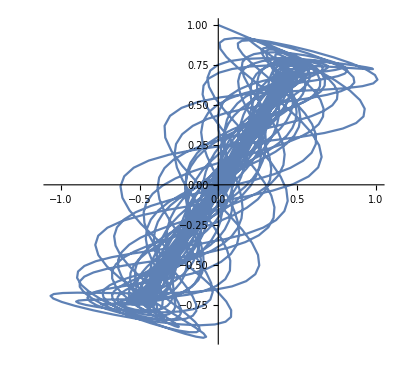

```mathematica
ParametricPlot[({x[t],y[t]}/.analsol),{t,0,100}]
```

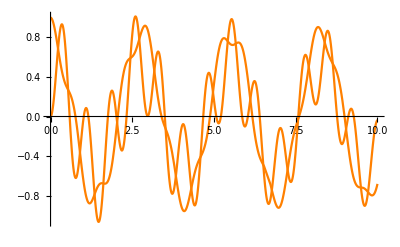

```mathematica
Plot[Through[({x,y}/.analsol)[t]],{t,0,10},PlotStyle->{Blue,Orange}]
```